```mathematica
List100 = {{"Static",0.085},{"Dynamic",0.166},{"Dynamic 5",0.068},{"Dynamic 10",0.059},{"Dynamic 20",0.070},{"Guided 1",0.121},{"Guided 2",0.114},{"Guided 3",0.103}};
List1000 = {{"Static",1.532},{"Dynamic",1.586},{"Dynamic 5",1.044},{"Dynamic 10",0.998},{"Dynamic 20",0.981},{"Guided 1",1.631},{"Guided 2",1.631},{"Guided 3",1.620}};
List5000 = {{"Static",43.07},{"Dynamic",39.67},{"Dynamic 5",38.63},{"Dynamic 10",40.08},{"Dynamic 20",38.28},{"Guided 1",53.27},{"Guided 2",53.60},{"Guided 3",55.077}};
```

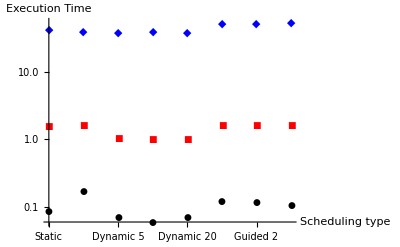

```mathematica
ListLogPlot[{List100,List1000,List5000}/.{"Static"->1,"Dynamic"->2,"Dynamic 5"->3, "Dynamic 10"->4,"Dynamic 20"->5 ,"Guided 1"->6,"Guided 2"->7, "Guided 3"->8},AxesLabel->{"Scheduling type","Execution Time"},PlotRange->All, PlotMarkers->Automatic,ImageSize->400,PlotStyle->{{Thick,Black},{Thick,Red},{Thick,Blue}},Ticks->{{{1,"Static"},{2,"Dynamic"},{3,"Dynamic 5"},{4,"Dynamic 10"},{5,"Dynamic 20"},{6,"Guided 1"},{7,"Guided 2"},{8,"Guided 3"}},Automatic}]
```

{a→40.3069,b→-0.104801}

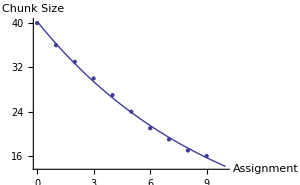

```mathematica
GuidedList={{0,40},{1,36},{2,33},{3,30},{4,27},{5,24},{6,21},{7,19},{8,17},{9,16}};
model = a Exp[b x];
fit =FindFit[GuidedList,model,{{a,40},b},x];
{a->40.306945117694625,b->-0.10480085529756422}
modelf = Function[{t},Evaluate[model/.fit]];
Show[ListPlot[GuidedList],Plot[modelf[t],{x,0,10}],AxesLabel->{"Assignment","Chunk Size"}, ImageSize->300]
```

```mathematica
seqList100 = {{1,1},{2,1.72/2.26},{3,2.47/2.26},{4,3.17/2.26},{6,4.32/2.26},{8,5.06/2.26},{10,1.74/2.26},{12,1.45/2.26},{16,1.08/2.26},{32,.61/2.26},{64,.36/2.26},{128,.16/2.26}};
threadList100 ={{1,1},{2,1.72/.888},{3,2.47/.888},{4,3.17/.888},{6,4.32/.888},{8,5.06/.888},{10,1.74/.888},{12,1.45/.888},{16,1.08/.888},{32,.61/.888},{64,.36/.888},{128,.16/.888}};
```

```mathematica
seqList1000 = {{1,1},{2,1.81/1.88},{3,2.70/1.88},{4,3.61/1.88},{6,5.37/1.88},{8,7.08/1.88},{10,4.44/1.88},{12,5.22/1.88},{16,6.13/1.88},{32,5.40/1.88},{64,5.14/1.88},{128,4.69/1.88}};
threadList1000 ={{1,1},{2,1.81/.903},{3,2.70/.903},{4,3.61/.903},{6,5.37/.903},{8,7.08/.903},{10,4.44/.903},{12,5.22/.903},{16,6.13/.903},{32,5.40/.903},{64,5.14/.903},{128,4.69/.903}};
```

```mathematica
seqList5000 = {{1,1},{2,1.80/1.925},{3,2.70/1.925},{4,3.60/1.925},{6,5.37/1.925},{8,7.08/1.925},{10,5.55/1.925},{12,6.35/1.925},{16,6.81/1.925},{32,6.54/1.925},{64,6.82/1.925},{128,6.80/1.925}};
threadList5000 ={{1,1},{2,1.80/.901},{3,2.70/.901},{4,3.60/.901},{6,5.37/.901},{8,7.08/.901},{10,5.55/.901},{12,6.35/.901},{16,6.81/.901},{32,6.54/.901},{64,6.82/.901},{128,6.80/.901}};
```

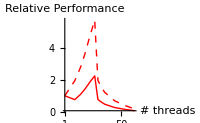

```mathematica
ListLogLinearPlot[{seqList100,threadList100},Joined->True,PlotStyle->{{Red,Thick},{Red,Dashed,Thick}},PlotRange->All,AxesLabel->{"# threads","Relative Performance"},ImageSize->200]
```

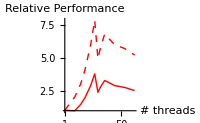

```mathematica
ListLogLinearPlot[{seqList1000,threadList1000},AxesOrigin->Automatic,Joined->True,PlotStyle->{{Red,Thick},{Red,Dashed,Thick}},PlotRange->All,AxesLabel->{"# threads","Relative Performance"},ImageSize->200]
```

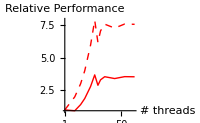

```mathematica
ListLogLinearPlot[{seqList5000,threadList5000},AxesOrigin->Automatic,Joined->True,PlotStyle->{{Red,Thick},{Red,Dashed,Thick}},PlotRange->All,AxesLabel->{"# threads","Relative Performance"},ImageSize->200]
```